Numerical Simulation of Quantum Field Fluctuations

Authors of paper: Emily R. Taylor, Samuel Yencho, L.H. Ford
Link to pre-print: https://arxiv.org/abs/2312.17155v1
Notebook: Óscar Amaro, December 2023

Introduction
In this notebook we reproduce some results from the paper. 
Main idea: imposition of correlation function on RNG, with application in quantum field fluctuations.

## Figure 1

```mathematica
Clear[f,a,b,t0,x,seq,Ct0lst,npoints,nsteps,i,x1,x2]

npoints=30;(*801;*)
nsteps=30000;(*20000;*)
seq=Table[0,{i,1,nsteps}];
Ct0lst=Table[0,{i,1,npoints}];

f=1/b ArcTan[(4-t0^2)/(4π^2 a(4+t0^2)^2)];(*eq 3.4 typo, should π^2*)
a=0.01404;
b=1.58;
t0lst =Table[7/npoints *j,{j,0,npoints-1}];
For[j=1,j<npoints,j++,
t0=t0lst[[j]];
x=RandomVariate[NormalDistribution[0,1]];
seq[[1]]=x;
For[i=1,i<nsteps,i++,
x=RandomVariate[NormalDistribution[0,1]]+ x f;(* if you take out the -x f term in the mean, an uncorrelated bi-gaussian could of points will be produced *)
seq[[i+1]]=x;
(*Print[i];*)
];
x1 =seq[[;;-2]];
x2 = seq[[2;;]];
Ct0lst[[j]]=Correlation[x1,x2];
(*ListPlot[Transpose[{x1,x2}],AspectRatio->1];
Mean[x1 x2];
CorrelationFunction[seq,1];
*)
]
```

(4-t0^2)/(4 π^2 (4+t0^2)^2)

0.00633257

1/(16 π^2)

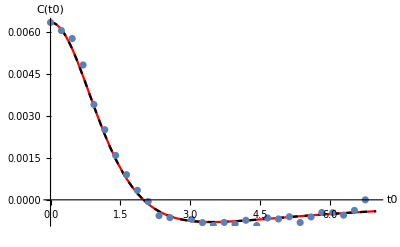

```mathematica
Clear[eq210,t0,f]
eq210=(4-t0^2)/(4π^2(t0^2+4)^2)
f=1/b ArcTan[(4-t0^2)/(4π^2 a(4+t0^2)^2)];
a=0.01404;
b=1.58;
a Tan[b f]/.{t0->0}
eq210/.{t0->0}
Show[{
Plot[{eq210,a Tan[b f]},{t0,0,7},PlotStyle->{Red,{Dashed,Black}},AxesLabel->{"t0","C(t0)"}],ListPlot[Transpose[{t0lst,Ct0lst/Ct0lst[[1]]*1/(16 π^2)}],Joined->False]}]
(* red - eq 2.10, dashed black - C(f(t0)), dots - sampled *)
```

## Figure 2

```mathematica
Clear[f,a,b,t0,x,seq,Kt0lst,npoints,nsteps,i,x1,x2]

npoints=70;(*801;*)
nsteps=30000;(*20000;*)
seq=Table[0,{i,1,nsteps}];
Kt0lst=Table[0,{i,1,npoints}];

f=1/b ArcTan[(1-6t0^2+t0^4)/(a(1+t0^2)^4)];
a=0.672;
b=1.59;
t0lst =Table[5/npoints *j,{j,0,npoints-1}];
For[j=1,j<npoints,j++,
t0=t0lst[[j]];
x=RandomVariate[NormalDistribution[0,1]];
seq[[1]]=x;
For[i=1,i<nsteps,i++,
x=RandomVariate[NormalDistribution[0,1]]+ x f;
seq[[i+1]]=x;
];
x1 =seq[[;;-2]];
x2 = seq[[2;;]];
Kt0lst[[j]]=Correlation[x1,x2];
]
```

(1-6 t0^2+t0^4)/((1+t0^2)^4)

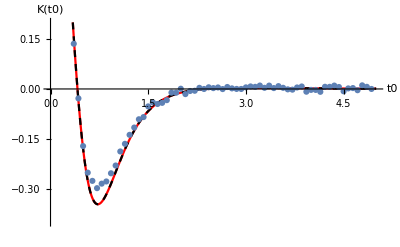

```mathematica
Clear[eq213,t0,a,b]
eq213=(1-6t0^2+t0^4)/((1+t0^2)^4)
f=1/b ArcTan[(1-6t0^2+t0^4)/(a(1+t0^2)^4)];
a=0.672;
b=1.59;
Show[{
Plot[{eq213,a Tan[b f]},{t0,0,5},PlotStyle->{Red,{Dashed,Black}},AxesLabel->{"t0","K(t0)"},PlotRange->{-0.4,0.2}],ListPlot[Transpose[{t0lst,Kt0lst}],Joined->False]}]
(* red - eq 2.13, dashed black - K(f(t0)), dots - sampled *)
```

## Figure 3

```mathematica
Clear[f,a,b,t0,x,seq,C1t0lst,npoints,nsteps,i,x1,x2]

npoints=70;(*801;*)
nsteps=30000;(*20000;*)
seq=Table[0,{i,1,nsteps}];
C1t0lst=Table[0,{i,1,npoints}];

f=1/b ArcTan[Cos[t0]/a];
a=0.672;
b=1.59;
t0lst =Table[4π/npoints *j,{j,0,npoints-1}];
For[j=1,j<npoints,j++,
t0=t0lst[[j]];
x=RandomVariate[NormalDistribution[0,1]];
seq[[1]]=x;
For[i=1,i<nsteps,i++,
x=RandomVariate[NormalDistribution[0,1]]+ x f;
seq[[i+1]]=x;
];
x1 =seq[[;;-2]];
x2 = seq[[2;;]];
C1t0lst[[j]]=Correlation[x1,x2];
]
```

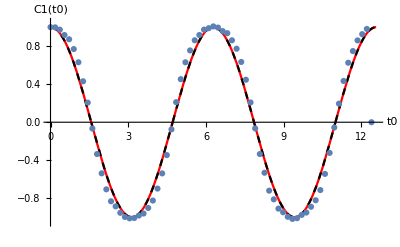

```mathematica
Clear[t,k,t0]
f=1/b ArcTan[Cos[t0]/a];
a=0.672;
b=1.59;

Show[{Plot[{Cos[ t0],a Tan[b f]},{t0,0,4π},AxesLabel->{"t0","C1(t0)"},PlotStyle->{Red,{Dashed,Black}},PlotRange->{-1.05,+1.05}]
,ListPlot[Transpose[{t0lst,C1t0lst/C1t0lst[[1]]}],Joined->False]}]
(* red - eq 2.13, dashed black - C1(f(t0)), dots - sampled *)
```